The MNSP matrix 

Calculations for the probability of finding the solar neutrino in the electron flavour upon reaching the Earth

```mathematica
(* Define the necessary variables *)

p = Array[ #&, 100, {10^4, 4*10^5}];
m21sqrd = 8.00*10^(-5);
m32sqrd = 2.40*10^(-3);
c = 2.99*10^8;
theta12 = 0.59;
theta13 = -11.5 * (Pi/180);
E12[p_] = m21sqrd * c^3 / (2*p);
E23[p_] = m32sqrd * c^3 / (2*p);
E13[p_] = m32sqrd * c^3 / (2*p);
t = 500;
hbar = 1.05*10^(-34);
norm = 1;
```

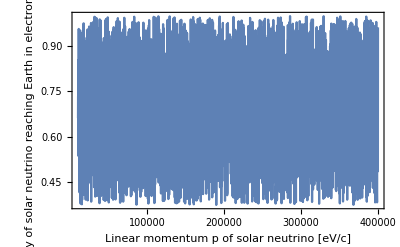

```mathematica
(* Probability calculation dependent on momentum *)

P= norm*((Cos[theta12]^4 + Sin[theta12]^4 )*Cos[theta13]^4+ 2*(Cos[E12*t/ hbar])*(Cos[theta12]^2)*(Sin[theta12]^2)*(Cos[theta13]^4 )+ 2*(Cos[E13*t/hbar])*(Cos[theta12]^2)*(Cos[theta13]^2)*(Sin[theta13]^2) + 2*(Cos[E23 * t / hbar])*(Sin[theta12]^2)*(Cos[theta13]^2)*(Sin[theta13]^2) + Sin[theta13]^4);
Pplot= norm*((Cos[theta12]^4 + Sin[theta12]^4 )*Cos[theta13]^4+ 2*(Cos[(m21sqrd * c^3 / (2*pp))*t/ hbar])*(Cos[theta12]^2)*(Sin[theta12]^2)*(Cos[theta13]^4 )+ 2*(Cos[(m32sqrd * c^3 / (2*pp))*t/hbar])*(Cos[theta12]^2)*(Cos[theta13]^2)*(Sin[theta13]^2) + 2*(Cos[(m32sqrd * c^3 / (2*pp)) * t / hbar])*(Sin[theta12]^2)*(Cos[theta13]^2)*(Sin[theta13]^2) + Sin[theta13]^4);

(* Generate plot *)

plot1 = Plot[Pplot, {pp, 10^4, 4*10^5}, Frame->True, FrameLabel->{"Linear momentum p of solar neutrino [eV/c]", "Probability of solar neutrino reaching Earth \n in electron flavour state"}, RotateLabel ->True]
```

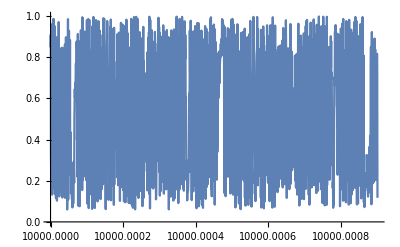

```mathematica
(* A closer look *)

plot2 = Plot[Pplot, {pp, 10^4, 1.00000009*10^4}]
```

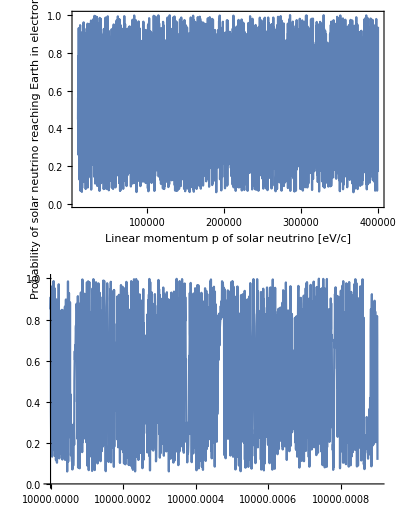

```mathematica
(* Combine plots *)

GraphicsColumn[{plot1, plot2}]
```

```mathematica
(* Determine the average value of the function Pplot *)

a = 10^4;
b = 4*10^5;
AveProbability = (1 / (b - a)) * Integrate[Pplot, {pp, a, b}]
```

0.686412

The MSW effect

```mathematica
Clear[E1, E2, E3, V]
```

Complete expression

```mathematica
Eigenvalues[{{E1 + V*(Cos[theta12]^2)*(Cos[theta13]^2), V*(Cos[theta12])*(Sin[theta12])*(Cos[theta13]^2), V*(Cos[theta12])*(Cos[theta13])*(Sin[theta13])}, {V*(Sin[theta12])*(Cos[theta12])*(Cos[theta13]^2), E2 + V*(Sin[theta12]^2)*(Cos[theta13]^2), V*(Sin[theta12])*(Cos[theta13])*(Sin[theta13])}, {V*(Cos[theta12])*(Cos[theta13])*(Sin[theta13]), V*(Sin[theta12])*(Cos[theta13])*(Sin[theta13]), E3+V*Sin[theta13]^2}}];
```

Third approximation

```mathematica
Clear[E3]
Eigenvalues[{{E1 + V*(Cos[theta12]^2), V*(Cos[theta12])*(Sin[theta12]), V*(Cos[theta12])*(Cos[theta13])*(Sin[theta13])}, {V*(Sin[theta12])*(Cos[theta12]), E2 + V*(Sin[theta12]^2), V*(Sin[theta12])*(Cos[theta13])*(Sin[theta13])}, {V*(Cos[theta12])*(Cos[theta13])*(Sin[theta13]), V*(Sin[theta12])*(Cos[theta13])*(Sin[theta13]), E3}}];
```

```mathematica
Eigenvectors[{{E1 + V*(Cos[th12]^2), V*(Cos[th12])*(Sin[th12]), V*(Cos[th12])*(Cos[th13])*(Sin[th13])}, {V*(Sin[th12])*(Cos[th12]), E2 + V*(Sin[th12]^2), V*(Sin[th12])*(Cos[th13])*(Sin[th13])}, {V*(Cos[th12])*(Cos[th13])*(Sin[th13]), V*(Sin[th12])*(Cos[th13])*(Sin[th13]), E3}}];
```

Second approximation (determines that \tilde{E3} \approx E3)

```mathematica
Eigenvalues[{{E1 + V*(Cos[theta12]^2), V*(Cos[theta12])*(Sin[theta12]), 0}, {V*(Sin[theta12])*(Cos[theta12]), E2 + V*(Sin[theta12]^2), 0}, {0, 0, E3}}]
```

{E3,0.5 (1. E1+1. E2+1. V-√(1. E1^2-2. E1 E2+1. E2^2+0.762141 E1 V-0.762141 E2 V+1. V^2)),0.5 (1. E1+1. E2+1. V+√(1. E1^2-2. E1 E2+1. E2^2+0.762141 E1 V-0.762141 E2 V+1. V^2))}

```mathematica
Eigenvectors[{{E1 + V*(Cos[theta12]^2), V*(Cos[theta12])*(Sin[theta12]), 0}, {V*(Sin[theta12])*(Cos[theta12]), E2 + V*(Sin[theta12]^2), 0}, {0,0, E3}}]
```

{{0,0,1.},{-1/V 1.08161 (-1. E1+1. E2-0.38107 V+1. √(1. E1^2-2. E1 E2+1. E2^2+0.762141 E1 V-0.762141 E2 V+1. V^2)),1.,0},{1/V 1.08161 (1. E1-1. E2+0.38107 V+1. √(1. E1^2-2. E1 E2+1. E2^2+0.762141 E1 V-0.762141 E2 V+1. V^2)),1.,0}}

```mathematica
Eigenvalues[{{E1 + V*(Cos[th12]^2), V*(Cos[th12])*(Sin[th12]), 0}, {V*(Sin[th12])*(Cos[th12]), E2 + V*(Sin[th12]^2), 0}, {0, 0, E3}}]
```

{E3,1/2 (E1+E2+V-√(E1^2-2 E1 E2+E2^2+V^2+2 E1 V Cos[2 th12]-2 E2 V Cos[2 th12])),1/2 (E1+E2+V+√(E1^2-2 E1 E2+E2^2+V^2+2 E1 V Cos[2 th12]-2 E2 V Cos[2 th12]))}

```mathematica
Eigenvectors[{{E1 + V*(Cos[th12]^2), V*(Cos[th12])*(Sin[th12]), 0}, {V*(Sin[th12])*(Cos[th12]), E2 + V*(Sin[th12]^2), 0}, {0,0, E3}}]
```

{{0,0,1},{-1/(2 V)Csc[th12] Sec[th12] (-E1+E2-V+√(E1^2-2 E1 E2+E2^2+V^2+2 E1 V Cos[2 th12]-2 E2 V Cos[2 th12])+2 V Sin[th12]^2),1,0},{1/(2 V)(-2 V+E1 Csc[th12]^2-E2 Csc[th12]^2+V Csc[th12]^2+√(E1^2-2 E1 E2+E2^2+V^2+2 E1 V Cos[2 th12]-2 E2 V Cos[2 th12]) Csc[th12]^2) Tan[th12],1,0}}

```mathematica
Eigenvectors[{{E1 + V*(Cos[theta12]^2), V*(Cos[theta12])*(Sin[theta12]), 0}, {V*(Sin[theta12])*(Cos[theta12]), E2 + V*(Sin[theta12]^2), 0}, {0,0, E3}}]
```

{{0,0,1.},{-1/V 1.08161 (-1. E1+1. E2-0.38107 V+1. √(1. E1^2-2. E1 E2+1. E2^2+0.762141 E1 V-0.762141 E2 V+1. V^2)),1.,0},{1/V 1.08161 (1. E1-1. E2+0.38107 V+1. √(1. E1^2-2. E1 E2+1. E2^2+0.762141 E1 V-0.762141 E2 V+1. V^2)),1.,0}}

Probability

```mathematica
(Sin[theta12]^2) * (Cos[theta13]^4 )+ Sin[theta13]^4
```

0.287